```mathematica
(*Styling of the text*)
s=Directive[FontSize->Large,FontFamily->"Linux Libertine Display"];
st[text_]:=Style[text,s];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

## Hamiltonians

### Definitions

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

## ρ dependance of λ and λb

```mathematica
ω=(√5-1)/2//N;
(* interference factor *)
gam[ρ_,q_]:=1/(1+ρ^q);
(* molecular and atomic renormalization factors *)
lamb[ρ_]:=((1+gam[ρ,1.] ρ^2-√(1+(gam[ρ,1.] ρ^2)^2))/(2gam[ρ,1.] ρ^2));
barlamb[ρ_]:=((√((1+ρ^2)^4+4 ρ^4)-(1+ρ^2)^2)/(2 ρ^4));
```

```mathematica
λb[ρ_]:=2/((1+ρ^2)^2+Sqrt[(1+ρ^2)^4+4ρ^4]);
λ[ρ_,q_]:=1/(1+ρ^2gam[ρ,q]+Sqrt[1+(ρ^2gam[ρ,q])^2]);
λ[ρ_]:=λ[ρ,1.];
```

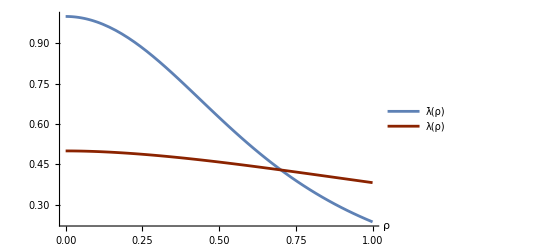

```mathematica
Plot[{λb[ρ],λ[ρ]},{ρ,0,1},AxesLabel->{"ρ"},PlotLegends->st/@{"λ̄(ρ)","λ(ρ)"},PlotStyle->{{AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[2],comp}},AxesStyle->Directive[FontSize->15,FontFamily->"CMU Serif"]]
```

```mathematica
Export[NotebookDirectory[]<>"lb_lbb.pdf",%]
```

/home/nicolas/git/talks/CMAC Days Grenoble 2015/lb_lbb.pdf

## Numerical computation of λ and λb using D_(+∞)

### Definitions concerning the fractal exponents

We define general functions computing fractal dimensions from lists, rather than functions adapted to our specific case.

We compute χ_q^n(i)=Σ_a|ψ^n(i,a)|^(2q).
We define the local dimension of the wavefunctions:
D_q(i)=lim_(n→∞) 1/(q-1)(log(χ_q^n(i)))/(log(1/F_n))

```mathematica
(* wf is a list of numbers that are a priori the coefficients of a wavefunction. They can be coefficients in the position basis, for a given energy, or coefficients in the energy basis for a particular position. *)
WfD[int_,q_]:=-(q-1)^-1 Log[Plus@@(int^q)]/Log[Length@int];
```

```mathematica
(* a more precise way of computing the dimensions, using data from two systems of consecutive size *)
tauqxloc[int_,intN_,q_]:=-Log[(Total@(int^q))/(Total@(intN^q))]/Log[(Length@int)/(Length@intN)];
```

We compute the partition function (Γ_(τ,q))^n(i)=Σ_a(|ψ^n(i,a)|^(2q))/((Δ_a^n)^τ).
We define the local dimension of the wavefunctions:
τ_i(q) such that lim_(n→∞) ((Γ_(τ_i(q),q))^(n+1)(i))/((Γ_(τ_i(q),q))^n(i))=1

```mathematica
(* compute fractal dimension Subscript[D, q] from 2 lists of weights and box lengths, using the thermodynamic formalism *)
PartD[weights_,weightsN_,lengths_,lengthsN_,q_]:=Block[{gam,gamN,τ,τ0,q0},
gam=Plus@@((weights)^q0(lengths)^-τ);
gamN=Plus@@((weightsN)^q0(lengthsN)^-τ);
(* Subscript[D, q] *)
τ0=τ/.FindRoot[(gamN/gam/.q0->q)-1,{τ,0}];
τ0/(q-1)
]
```

#### Tree structure

After a renormalization step, a given site i of the n^th approximant becomes either molecular (in which case n becomes n-2) or atomic (n becomes n-3). 
We can thus associate to each site a unique “renormalization path”: the sequence of molecular/atomic sites that has led to it, starting from the trivial (F_n=1) chain and inflating it.

More details in the “renormalization_path.nb” file.

```mathematica
(* take a renormalization path (seq), a site label (i) and an approximant size (n) and return the new renormalization path, the new site label and the new size after one renormalization group operation *)
ClearAll[i,n];
iterSeq[{seq_,i_,n_}]:=Block[{inew=i,seqn=seq,nnew=n},
If[i>Fibonacci[n-1],seqn="m"<>seq;inew=i-Fibonacci[n-1];nnew=n-2;,
If[i>Fibonacci[n-2],seqn="a"<>seq;inew=i-Fibonacci[n-2];nnew=n-3,
seqn="m"<>seq;nnew=n-2;]];
{seqn,inew,nnew}
]

(* false when n<3 *)
test=#[[3]]≥3&;
(* take a site (i), a size (n) and return the renormalization path for this site *)
path[i_,n_]:=NestWhile[iterSeq,{"",i,n},test][[1]]
(* compute the relative time spent on molecular sites (x) *)
xPath[i_,n_]:={i,StringCount[NestWhile[iterSeq,{"",i,n},test][[1]],"m"]/n}
(* generate the whole (x) tree! *)
tree[n_]:=xPath[#,n]&/@ Range[Fibonacci[n]]
```

```mathematica
paths[n_]:=path[#,n]&/@Range[Fibonacci[n]]
```

```mathematica
(* count the numbers Subscript[n, A] and Subscript[n, M] *)
count[n_]:=Transpose[StringCount@@@({paths[n],#}&/@{"m","a"})]
```

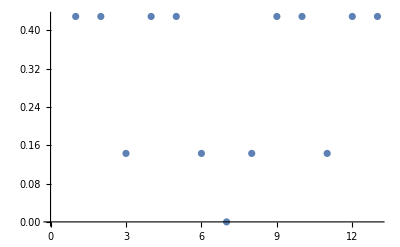

```mathematica
ListPlot[tree[7],Joined->False]
```

```mathematica
MapThread[2#1+3#2&,Transpose[count[9]]]
```

{8,8,7,8,8,7,8,7,8,8,7,8,8,7,8,7,8,8,7,8,7,8,8,7,8,8,7,8,7,8,8,7,8,8}

### Numerical tests: can we compute D_(+∞) selecting only the largest component of the wavefunction?

Fix a system size, we want to compute D_(+∞)(x) for several values of ρ, and then compare with the theoretical predictions.

First, let us try to compute D_q for increasing values of q, to see the convergence

```mathematica
(* keep at least one processor free to prevent freeze *)
LaunchKernels[$ProcessorCount];
```

```mathematica
n=17;
ρ=0.15;
tol=10^-14;
(* compute wavefunctions and energies *)
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec=vec[[Ordering[val]]];
(* drop small components *)
(*vec=Chop[vec,tol];*)

(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);

(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;
```

```mathematica
(* compute D_(+∞) brute-force style, ie by taking some q >> 1 *)
qRange=Range[0.1,100,1.];
(* Subscript[D, q](0) for large qs *)
wf0=vec[[listPos[[1,1]]]];
Dq0=ParallelMap[WfD[wf0,#]&,qRange];
```

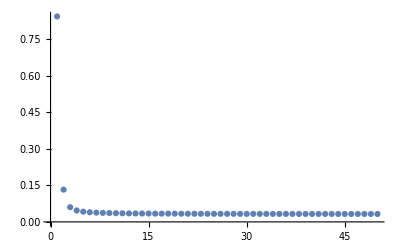

```mathematica
ListPlot[Dq0,PlotRange->All]
```

```mathematica
(* Subscript[D, q](1/2) for large qs *)
wfmol=vec[[listPos[[-1]]]];
avWfD[wfl_,q_]:=Block[{dl},
dl=Map[WfD[#,q]&,wfl];
Mean[dl]
]
Dqmol=ParallelMap[avWfD[wfmol,#]&,qRange];
```

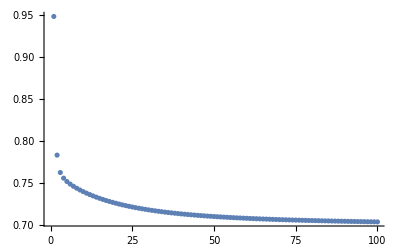

```mathematica
ListPlot[Dqmol,PlotRange->All]
```

It seems that for both x = 0, 1/2 the q -> D_q function converges nicely as q increases.
Now, let us try to compute directly D_(+∞) using that taking q -> ∞ selects the largest component(s) of the wavefunction, and see if we get the correct asymptotic value.

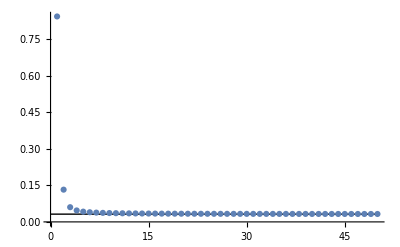

```mathematica
(* select the largest component of the x=0 wavefunction *)
wf0max=Max[wf0];
(* compute the associated exponent *)
Dinf0=-2Log[Abs[wf0max]]/Log[Fibonacci[n+2]];
ListPlot[Dq0,PlotRange->All,Epilog->Line[{{0,Dinf0},{Max[qRange]+1,Dinf0}}]]
```

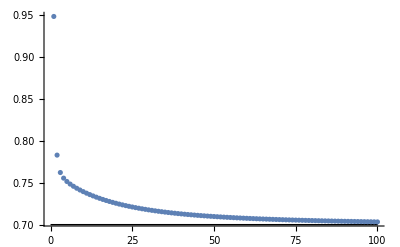

```mathematica
(* select the largest components of the x=1/2 wavefunctions *)
wfmolmax=Max/@wfmol;
(* compute the associated exponents *)
Dinfmols=-2Log[Abs[#]]/Log[Fibonacci[n+2]]&/@wfmolmax;
(* take the average *)
Dinfmol=Mean[Dinfmols];
ListPlot[Dqmol,PlotRange->All,Epilog->Line[{{0,Dinfmol},{Max[qRange]+1,Dinfmol}}]]
```

Conclusion:
Although the convergence is very slow for the molecular states, the results compare well in both cases. We will chose the compute D_(+∞) using the “largest coefficient” method because it is much faster.

Rk: convergence is slow for molecular states, because these states have a lot of components of about the same amplitude.

### Compare with theory, without finite-size corrections

```mathematica
(* theoretical expression *)
Dinf[ρ_,x_]:=(x Log[λ[ρ]]+(1-2x)/3Log[λb[ρ]])/Log[ω]
```

```mathematica
Dinflist[ρ_]:=Table[Dinf[ρ,x],{x,0,0.5,0.1}];
```

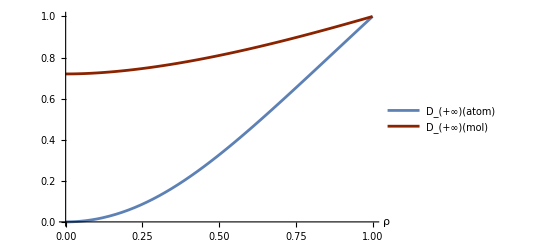

```mathematica
Plot[{Dinf[ρ,0],Dinf[ρ,1/2]},{ρ,0,1},AxesLabel->{"ρ"},PlotLegends->st/@{"D_(+∞)(atom)","D_(+∞)(mol)"},PlotStyle->{{AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[2],comp}},AxesStyle->Directive[FontSize->15,FontFamily->"CMU Serif"]]
```

```mathematica
(* numerics! *)

(* return the eigenvectors *)
vecs[n_,ρ_]:=Block[{val,vec},
(* compute wavefunctions and energies *)
{val,vec}=Eigensystem[hp[n,ρ,1.]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]]

(* return the positions ordered by increasing value of x, size n+2 *)
listPos[n_]:=Block[{ xlist, xvalues, listPos},
(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);

(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;
listPos]

(* returns the average D_(+∞) for a list of wavefunctions *)
dinf[wfs_, n_]:=Block[{wfsmax, dinfs},
(* select the largest component for each wf *)
wfsmax=Max/@Abs[wfs];
(* compute the associated exponents *)
dinfs=-2Log[Abs[#]]/Log[Fibonacci[n+2]]&/@wfsmax;

Mean[dinfs]
]
```

```mathematica
n=17;
(* list all positions, sorted by increasing value of x *)
pos=listPos[n];
(* iterate over ρ *)
ρRange=Range[0.01,1.01,0.1];
(* compute the wf for each value of ρ *)
wfs=ParallelMap[vecs[n,#]&,ρRange];
(* x=0 wfs *)
wfs0=Table[wfs[[i,pos[[1]]]],{i,Length[wfs]}];
(* x=1/2 wfs *)
wfsMol=Table[wfs[[i,pos[[-1]]]],{i,Length[wfs]}];
```

```mathematica
(* dinfs x=0 *)
d0s=dinf[#,n]&/@wfs0;
(* dinfs x=1/2 *)
dMols=dinf[#,n]&/@wfsMol;
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

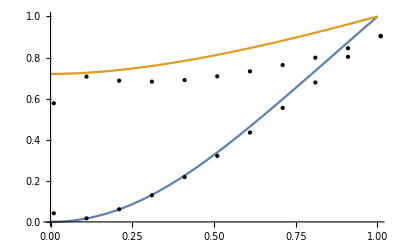

```mathematica
Plot[{Dinf[ρ,0],Dinf[ρ,1/2]},{ρ,0,1},Epilog->(Point[glue[ρRange,#]]&/@{d0s,dMols})]
```

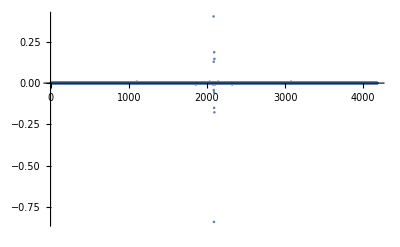

```mathematica
ListPlot[wfs0[[1]],PlotRange->All]
```

### With finite-size corrections

In the quasiperiodic limit,
D_(+∞)=x Log λ + (1-2x)/3 Log λb, where Log is the base ω log.

Finite-size effects affect the coefficients in front of the logs:
D_(+∞, n) =nm/n Log λ + na/n Log λb , where nm and na are resp the number of molecular/atomic inflation operations needed to construct the state ψ at hand from a state on the trivial n=1 chain. 
Another effect of the finite-size is that ω -> 1/F_n^(1/n). All in all,
D_(+∞, n)= nm Log λ / Log F_n + na Log λb / Log 1/F_n.

```mathematica
count[n_]:=Transpose[Apply[StringCount,({paths[n],#1}&)/@{"m","a"},{1}]]
```

```mathematica
(* list the possible couples (nm, na) for every state on the chain *)
DeleteDuplicates[count[n+2]]
```

{{9,0},{7,1},{6,2},{4,3},{3,4},{1,5},{0,6}}

```mathematica
(* number of molecular deflations for x = 1/2 *)
nm=9;
(* number of atomic deflations for x = 0 *)
na=6;
```

```mathematica
(* theoretical expression *)
Dinfn[ρ_,x_,nm_,na_, n_]:=-(nm Log[λ[ρ]]+na Log[λb[ρ]])/Log[Fibonacci[n+2]]
```

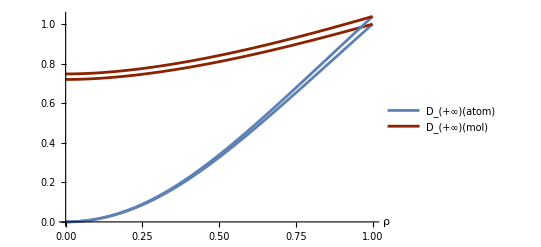

```mathematica
Plot[{Dinf[ρ,0],Dinf[ρ,1/2], Dinfn[ρ,0,0,na,n],Dinfn[ρ,1/2,nm,0,n]},{ρ,0,1},AxesLabel->{"ρ"},PlotLegends->st/@{"D_(+∞)(atom)","D_(+∞)(mol)"},PlotStyle->{{AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[2],comp}},AxesStyle->Directive[FontSize->15,FontFamily->"CMU Serif"]]
```

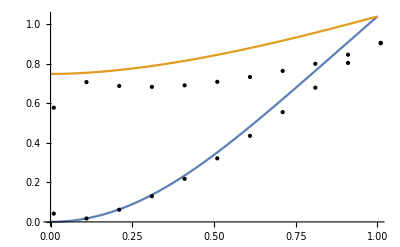

```mathematica
Plot[{Dinfn[ρ,0,0,na,n],Dinfn[ρ,1/2,nm,0,n]},{ρ,0,1},Epilog->(Point[glue[ρRange,#]]&/@{d0s,dMols})]
```

### With finite-size corrections and q finite

```mathematica
(* theoretical expression *)
Dinf[ρ_,x_]:=(x Log[λ[ρ]]+(1-2x)/3Log[λb[ρ]])/Log[ω]
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
Dq[ρ_,x_,q_,na_,nm_,n_]:=-(1/(q-1))(nm Log[λ[ρ]^q/λ[ρ^q,q]]+na Log[λb[ρ]^q/λb[ρ^q]])/(Log[Fibonacci[n+2]])
```

```mathematica
(* return the intensities, sorted by incresaing energy *)
sortedInts[n_,k_,ρ_]:=Block[{val,vec},
{val,vec}=Eigensystem[hk[k,n,ρ,1.]];
Abs[vec[[Ordering[val]]]]^2
]

ints[n_,ρ_]:=Block[{ints, ks,L=5},
ks=π Range[0,L-1,1]/(L-1);
(* compute wavefunctions and energies *)
ints=Map[sortedInts[n,#,ρ]&,ks];

Apply[Plus,ints]/L
]

(* return the positions ordered by increasing value of x, size n+2 *)
listPos[n_]:=Block[{ xlist, xvalues, listPos},
(* compute x for each site *)
xlist=tree[n+2];
(* drop the site labels, they are unecessary as x is indexed by increasing x label *)
xlist=Last@(Transpose[xlist]);

(* list all possible values of x *)
xvalues=Sort@DeleteDuplicates[xlist];
(* list all positions by increasing value of x *)
listPos=Flatten[Position[xlist,#]]&/@xvalues;
listPos]

(* returns the average Subscript[D, q] for a list of wavefunctions *)
dq[ints_,n_]:=Block[{ dinfs},
(* compute the associated exponents *)
(*dinfs=WfD[#,q]&/@ints;*)
dinfs=Max/@ints;
dinfs=-Log[dinfs]/Log[Fibonacci[n+2]];

If[Length[dinfs]>1,{Mean[dinfs], StandardDeviation[dinfs]},dinfs[[1]]]
]

(* return all the D_(+∞)'s for a list a wavefunctions *)
disp[ints_,n_]:=Block[{ dinfs},
dinfs=Max/@ints;
dinfs=-Log[dinfs]/Log[Fibonacci[n+2]];

dinfs
]
```

```mathematica
n=17;
(* list all positions, sorted by increasing value of x *)
pos=listPos[n];
(* iterate over ρ *)
ρRange=Range[0.1,1.01,0.1];
(* compute the wf for each value of ρ *)
wfs=ParallelMap[ints[n,#]&,ρRange];
(* x=0 wfs *)
wfs0=ParallelTable[wfs[[i,pos[[1]]]],{i,Length[wfs]}];
(* x=1/2 wfs *)
wfsMol=ParallelTable[wfs[[i,pos[[-1]]]],{i,Length[wfs]}];
(* edge of the spectrum wf *)
wfsEd=ParallelTable[wfs[[i,{1,-1}]],{i,Length[wfs]}];
(* max at the edge *)
wfsM=Table[Max[wfsEd[[i,1]]],{i,Length[wfs]}];
```

```mathematica
(* dinfs x=0 *)
dq0s=dq[#,n]&/@wfs0;
(*(* dinfs x=1/2 *)
dqMols=dq[#,qm,n]&/@wfsMol;
(* dinfs edge *)
dqEds=dq[#,qm,n]&/@wfsEd;*)
(* max *)
dqMaxs=-Log[Abs[#]]/Log[Fibonacci[n+2]]&/@wfsM;
(* standard deviation around the edge *)
stdMaxs=dq[#,n][[2]]&/@wfsMol;
(* dipersion of the D_(+∞)(1/2) *)
dqDisp=disp[#,n]&/@wfsMol;
```

```mathematica
stdMaxs
```

{0.00260857,0.00808234,0.0138931,0.0187393,0.0220713,0.0236213,0.0233201,0.0212544,0.0203779,0.0013146}

```mathematica
dqMaxs
```

{0.718936,0.718346,0.735587,0.763157,0.79638,0.832569,0.870244,0.908578,0.945945,0.978134}

dq0/dqMol(ρ = 1, n = 14+2) = 0.90 while dq0/dqMol(ρ = 1, n = 17+2) = 0.92 -> finite-size effect vanish quite rapidly.

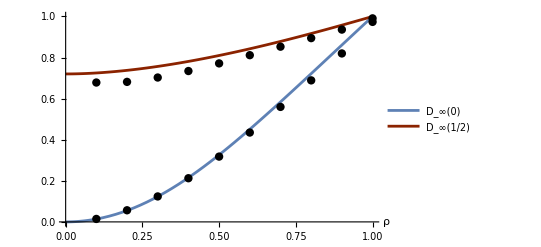

```mathematica
Plot[{Dinf[ρ,0],Dinf[ρ,1/2]},{ρ,0,1},Epilog->{PointSize[0.015],(Point[glue[ρRange,#]]&/@{dq0s,dqMaxs})},AxesLabel->{"ρ"},PlotLegends->st/@{"D_∞(0)","D_∞(1/2)"},PlotStyle->{{AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[2],comp}},AxesStyle->Directive[FontSize->15,FontFamily->"CMU Serif"]]
```

Plot the renormalization factors λ/λb

```mathematica
λnum=ω^(2dqMaxs);
λbnum=ω^(3dq0s);
λdisp=ω^(2 dqDisp);
ptsdisp=Flatten[Map[Function[u,{u[[1]],#}&/@u[[2]]],glue[ρRange,λdisp]],1];
δ=4;
stdλ=Transpose@{ω^(2(dqMaxs+δ stdMaxs)),ω^(2(dqMaxs-δ stdMaxs))};
```

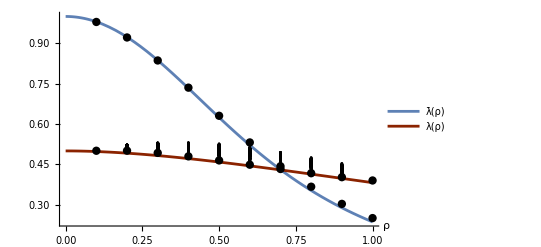

```mathematica
Plot[{λb[ρ],λ[ρ]},{ρ,0,1},Epilog->{{PointSize[0.015],(Point[glue[ρRange,#]]&/@{λnum,λbnum})},{PointSize[0.005],Point[ptsdisp]}},AxesLabel->{"ρ"},PlotLegends->st/@{"λ̄(ρ)","λ(ρ)"},PlotStyle->{{AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[2],comp}},AxesStyle->Directive[FontSize->15,FontFamily->"CMU Serif"]]
```

```mathematica
Export[NotebookDirectory[]<>"/renorm_th_num.pdf",%]
```

/home/nicolas/git/articles/fibonacci_multifractal/img//renorm_th_num.pdf

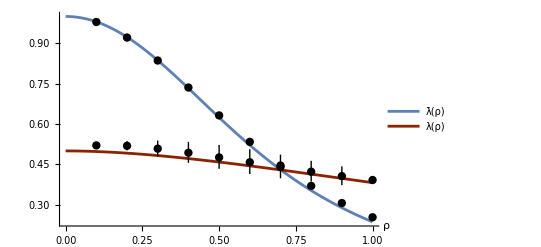

```mathematica
Plot[{λb[ρ],λ[ρ]},{ρ,0,1},Epilog->{PointSize[0.015],(Point[glue[ρRange,#]]&/@{λnum,λbnum}),Line[{{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}]&/@glue[ρRange,stdλ]},AxesLabel->{"ρ"},PlotLegends->st/@{"λ̄(ρ)","λ(ρ)"},PlotStyle->{{AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]},{AbsoluteThickness[2],comp}},AxesStyle->Directive[FontSize->15,FontFamily->"CMU Serif"]]
```

What about the q dependance of γ? We took γ(ρ,q) = 1/(1+ρ^q), and while this is justified for q=0, q=1, in the q->∞ limit it is clearly wrong that γ->0 for ρ finite. So the correct q-dependance of γ in this limit remains to be understood.

```mathematica
d2th[ρ_,q_,x_,n_]:=-(n+2)(x Log[λ[ρ,q]^q]+(1-2x)/3 Log[λb[ρ]^q]+x Log[2])/((q-1)Log[Fibonacci[n+2]]);
(* in the finite size case, 3 Subscript[n, A]+ 2 Subscript[n, M] ≠ n, so that it is more accurate to replace x by Subscript[n, M] and Subscript[n, A] in the fractal dimensions *)
dfinite[ρ_,q_,{nm_,na_},n_]:=If[q<3,-(nm/(n+2) Log[λ[ρ,q]^q/λ[ρ^q,q]]+na/(n+2) Log[λb[ρ]^q/λb[ρ^q]])/((q-1)Log[Fibonacci[n+2]^(1/(n+2))]),d2th[ρ,q,nm/(n+2),n]];
```

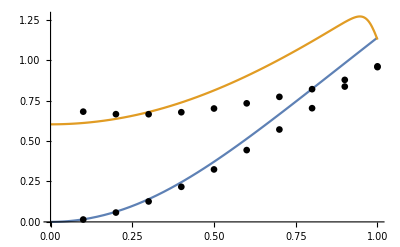

```mathematica
Plot[{dfinite[ρ,qm,{0,9},n],dfinite[ρ,qm,{6,0},n]},{ρ,0,1},Epilog->{PointSize[0.012],(Point[glue[ρRange,#]]&/@{dq0s,dqMols})}]
```

```mathematica
dfinite[ρ,qm,{0,na},n]
```

-0.015501 Log[lb[ρ]^50.]